```mathematica
(*Problem:Example 1.4 :1-D steady state solution in Cartesian coordinate. 
BC: at x=0, Subscript[T, 0]=37,x=0.04,Subscript[T, 1]=33,   Heat generation g: variable*)
```

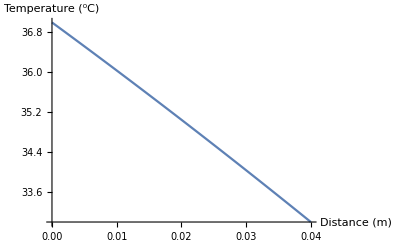

```mathematica
Clear["`*"]
Subscript[q, m]=100;
k=0.4;
Subscript[T, 0]=37;
Subscript[T, 1]=33;
solution1=NDSolve[{T''[x]+Subscript[q, m]/k== 0,T[0]==Subscript[T, 0],T[0.04]==Subscript[T, 1]},T,{x,0,0.04}];
PS=Plot[Evaluate[T[x]/.First[solution1]],{x,0,0.04},PlotRange->{{0,.04},{33,37}},AxesLabel->{"Distance (m)","Temperature (^0C)"}]
```

```mathematica
DSolve[T''[x]+Q== 0,T[x],x]
```

{{T[x]→-(Q x^2)/2+C[1]+x C[2]}}

```mathematica
Problem:Example 1.5 :1-D steady state solution in Cartesian coordinate. 
BC: at x=0, Subscript[T, 0]=37,x=0.04,Subscript[T, 1]=33,Subscript[T, a]=37   Heat generation g: variable
```

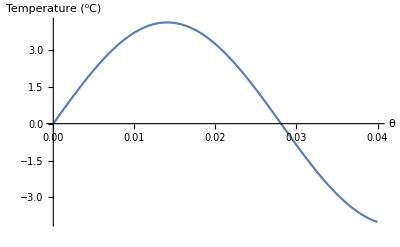

```mathematica
Subscript[m, b]=100;
Subscript[c, b]=50;
k=0.4;
γ=Sqrt [Subscript[m, b]*Subscript[c, b]/k];
Subscript[T, 0]=37;
Subscript[T, 1]=33;
Subscript[T, a]=37;
Subscript[θ, 0]=Subscript[T, 0]-Subscript[T, a];
Subscript[θ, 1]=Subscript[T, 1]-Subscript[T, a];
solution1=NDSolve[{θ''[x]+γ^2 *θ[x]== 0,θ[0]==Subscript[θ, 0],θ[0.04]==Subscript[θ, 1]},θ,{x,0,0.04}];
PS=Plot[Evaluate[θ[x]/.First[solution1]],{x,0,0.04},PlotRange->All,AxesLabel->{"x","θ (^0C)"}]
```

```mathematica
Problem:Example 1.4 :1-D steady state solution in Cylindrical coordinate. 
BC: at x=0, Subscript[T, 0]=37,x=0.04,Subscript[T, 1]=33,   Heat generation g: variable
```

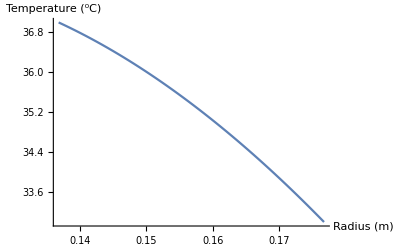

```mathematica
ClearAll[Evaluate[Context[]<>"*"]];
Subscript[q, r]=1000;
k=0.4;
Subscript[T, 0]=37;
Subscript[T, 1]=33;
Subscript[r, 1]=0.1368;
Subscript[r, 2]=0.1768;
solution1=NDSolve[{1/r * D[( r  *T'[r]), r]+Subscript[q, r]/k== 0,T[Subscript[r, 1]]==Subscript[T, 0],T[Subscript[r, 2]]==Subscript[T, 1]},T,{r,Subscript[r, 1],Subscript[r, 2]}];
PS=Plot[Evaluate[T[r]/.First[solution1]],{r,Subscript[r, 1],Subscript[r, 2]},PlotRange->Automatic,AxesLabel->{"Radius (m)","Temperature (^0C)"}]
```

```mathematica
DSolve[1/r * D[( r  *T'[r]), r]+A== 0,T[r],r]
```

{{T[r]→-(A r^2)/4+C[2]+C[1] Log[r]}}

```mathematica
Problem:Example 1.5 :1-D steady state solution in Cylindrical coordinate. 
BC: at x=0, Subscript[T, 0]=37,x=0.04,Subscript[T, 1]=33,   Heat generation g: variable
```

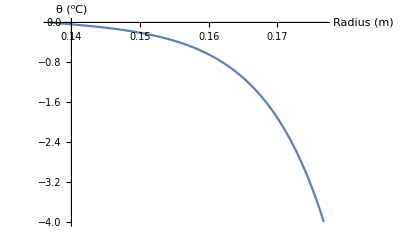

```mathematica
Subscript[m, b]=100;
Subscript[c, b]=50;
k=0.4;
γ=Sqrt [Subscript[m, b]*Subscript[c, b]/k];
Subscript[T, 0]=37;
Subscript[T, 1]=33;
Subscript[T, a]=37;
Subscript[θ, 0]=Subscript[T, 0]-Subscript[T, a];
Subscript[θ, 1]=Subscript[T, 1]-Subscript[T, a];
Subscript[r, 1]=0.1368;
Subscript[r, 2]=0.1768;
solution2=NDSolve[{θ''[r]+1/r *θ'[r] - γ^2 *θ[r]== 0,θ[Subscript[r, 1]]==Subscript[θ, 0],θ[Subscript[r, 2]]==Subscript[θ, 1]},θ,{r,Subscript[r, 1],Subscript[r, 2]}];
PS=Plot[Evaluate[θ[r]/.First[solution2]],{r,Subscript[r, 1],Subscript[r, 2]},PlotRange->All,AxesLabel->{"Radius (m)","θ (^0C)"}]
```

```mathematica
(*DSolve[θ''[r]+1/r *θ'[r] - M^2 *θ[r]== 0,θ[r],r]*)
Clear [m]
DSolve[{θ''[r]+1/r *θ'[r] - m^2 *θ[r]== 0,θ[r1]== t0, θ[r2]==t1},θ[r],r]
```

{{θ(r)→(-t1 0-ⅈ m r 0ⅈ m r1+t1 0ⅈ m r 0-ⅈ m r1+t0 0-ⅈ m r 0ⅈ m r2-t0 0ⅈ m r 0-ⅈ m r2)/(0-ⅈ m r1 0ⅈ m r2-0ⅈ m r1 0-ⅈ m r2)}}